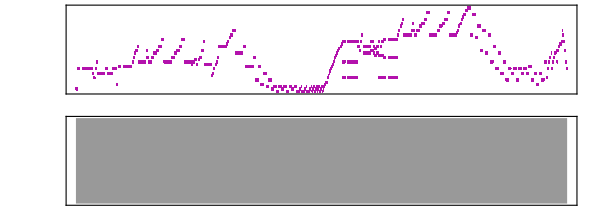

```mathematica
note[b_,x0_,t_,v_]:=Module[{a=b},Which[x0=="1",AppendTo[a,SoundNote[0,t,SoundVolume->v]],x0=="2",AppendTo[a,SoundNote[2,t,SoundVolume->v]],x0=="3",AppendTo[a,SoundNote[4,t,SoundVolume->v]],x0=="4",AppendTo[a,SoundNote[5,t,SoundVolume->v]],x0=="5",AppendTo[a,SoundNote[7,t,SoundVolume->v]],x0=="6",AppendTo[a,SoundNote[9,t,SoundVolume->v]],x0=="7",AppendTo[a,SoundNote[11,t,SoundVolume->v]],x0=="0",AppendTo[a,SoundNote[None,t,SoundVolume->v]],x0=="-",a[[-1,2]]+=t,x0=="_",
a[[-1,2]]/=2,x0=="*",
a[[-1,2]]*=1.5,x0=="t",
a[[-1,2]]/=3,x0=="%",
a[[-1,2]]/=5,x0==".",
a[[-1,1]]-=12,x0=="'",
a[[-1,1]]+=12,x0=="#",
a[[-1,1]]+=1,x0=="b",
a[[-1,1]]-=1];a];noteh[b_,x0_]:=Module[{h=b},Which[x0=="1",AppendTo[h,0],x0=="2",AppendTo[h,2],x0=="3",AppendTo[h,4],x0=="4",AppendTo[h,5],x0=="5",AppendTo[h,7],x0=="6",AppendTo[h,9],x0=="7",AppendTo[h,11],x0==".",h[[-1]]-=12,x0=="'",h[[-1]]+=12,x0=="#",h[[-1]]+=1,x0=="b",h[[-1]]-=1];h];PlaySheet[s_,t_,x_]:=Module[{lh=StringLength[x],xx=x,a={},v=1,par=False,h={},i,x0},For[i=1,i≤lh,i++,x0=StringTake[xx,1];If[par,If[x0==")",AppendTo[a,SoundNote[h,t,SoundVolume->v]];par=False;h={},h=noteh[h,x0]],If[x0=="(",par=True,v=Which[x0=="pm",0.8,x0=="p",0.5,x0=="p",0.2,x0=="fm",1.3,x0=="f",1.6,x0=="ff",2,x0=="n",1,True,v];
a=note[a,x0,t,v]]];xx=StringDrop[xx,1]];Sound[Prepend[a,s],{0,Plus@@(#[[2]]&/@a)}]];


PlaySheet["Violin",0.8,
"pp6.__|pm4#_0_4#-3__2__4#__6__|3*4#_p3pm4#_*p7.__|pm5_0_n55_*6__fm7__1#'__2'__3'__|66_7_t2'_t7_tn6_fm7_1#'_2'_|f3'_5'_66_7_1#'_2'_3'_5'_66t5#t6t6#t6bt6#t|7t2't4#'t5#5#__2#__3__4#__5#__6__7__3'__|3'3'__3#'__4#'__5#'__6'_7'__0___7'___1#'|1#'_3'__0___3'___5|5_7__0___7___1#_5__0___5___|7._3__0___3___7b._1#__0___1#___6._7b.__0___7b.___5#._7b.__0___7b.___|6._7b.__0___7b.___5#._7b.__0___7b.___6._7b.__0___7b.___5#._6.__0___7b.___|5#._6.__0___7b.___5#._6.__0___7b.___5#._t6._t7b._t5#.t_6.t_7b._t5#.t_6.t_7b._t5#.t_6.t_7b._t|5#.t_6.t_7b.t_7.t_7#.t_1t_2t_2#t_3t_3#t_4#t_5t_5#t_6t_7bt_7t_1't_1#'t_2'__2#'__3'__3#'__|(264#')_0_(264#')-3'____4#'____3'___2'__4#'__6'__|(1#'3')*(2'4#')_(1#'3')t(7#2#')t(1#'3')t(21'4#')t(21'3')t(21'4#')t|(275')_0_(275')(275')_*6'__7'__1#''__2''__3''__|6'*7't_2''t_7't_6'_7'_1#''_2''_|3''_5''_6'*7'_1#''_2''_|3''_5''_6'6'__6#'__7'__1#''__2''__3''__4''__4#''__|f5#''_6''__0___6''___6'_4#''__0___4#''___5#'_1#''__0___1#''___2'_7'__0___7'___|1#'_6'__0___6'___6_3'__0___3'___fm4#_1#'__0___1#'___3_6__0___6___|n1#_4#__0___4#___3_4#__0___4#___1#_4#__0___4#___3_4#__0___4#___
3_5__0___5___1#_3__0___3___7._3__0___3___1#_6__0___6___2t_4#t_6t_7t1#'t_4#t_6t_7t_1#'t2't_6t_2't_3't_3#'t4#'t_7't_6't_4#'t_2't_6t_4#t_"]
```